```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/robyn/Documents/Research/KLStats/Isochrone/WithGaiaErrors/RedGiants

Frequencies as a function of the actions

```mathematica
Mtrue=12.2;
btrue=8.0;
OmegaR[Jr_,L_]:=Mtrue^2/(2(Jr+(L+Sqrt[L^2 + 4 Mtrue btrue])/2)^2)
OmegaTheta[Jr_,L_]:=(1+L/Sqrt[L^2+4 Mtrue btrue])/2 (Mtrue^2/(2(Jr+(L+Sqrt[L^2 + 4 Mtrue btrue])/2)^2))
```

Conversion factor between km/s and kpc/Myr

```mathematica
kmsTokpcMyr=0.001022729843472133;
```

Construct streams as clumps in (Jr, L, L_z) space

```mathematica
Ns=10;
sigmas=RandomReal[{0,.01},Ns]
inclinations=RandomVariate[UniformDistribution[{-π,π}],Ns]
```

{0.00585076,0.00485581,0.00340855,0.00948766,0.000814968,0.00496225,0.00910957,0.00877644,0.00435041,0.0020401}

{1.28389,-0.620164,-0.31959,2.81376,-0.328417,-2.49413,0.24369,-2.97585,0.326174,2.00188}

```mathematica
spikyDist=MixtureDistribution[RandomReal[{0.1,1},Ns],Table[MultinormalDistribution[{RandomReal[{-1,1}],RandomReal[{2,10}],RandomReal[{0,10}]},DiagonalMatrix[{sigmas[[i]]/2,sigmas[[i]],sigmas[[i]]}]],{i,1,Ns}]]
```

MixtureDistribution[{0.813235,0.334927,0.692497,0.491671,0.964847,0.795718,0.523332,0.637937,0.766076,0.188128},{MultinormalDistribution[{0.397087,8.14864,4.08212},{{0.00292538,0.,0.},{0.,0.00585076,0.},{0.,0.,0.00585076}}],MultinormalDistribution[{-0.026561,6.99756,6.90921},{{0.00242791,0.,0.},{0.,0.00485581,0.},{0.,0.,0.00485581}}],MultinormalDistribution[{-0.963446,5.34331,8.8348},{{0.00170427,0.,0.},{0.,0.00340855,0.},{0.,0.,0.00340855}}],MultinormalDistribution[{-0.462637,3.12416,1.3854},{{0.00474383,0.,0.},{0.,0.00948766,0.},{0.,0.,0.00948766}}],MultinormalDistribution[{0.525467,9.23472,2.48285},{{0.000407484,0.,0.},{0.,0.000814968,0.},{0.,0.,0.000814968}}],MultinormalDistribution[{0.837507,8.94928,1.52366},{{0.00248113,0.,0.},{0.,0.00496225,0.},{0.,0.,0.00496225}}],MultinormalDistribution[{0.779381,3.65673,8.83027},{{0.00455479,0.,0.},{0.,0.00910957,0.},{0.,0.,0.00910957}}],MultinormalDistribution[{-0.437469,2.44188,0.672519},{{0.00438822,0.,0.},{0.,0.00877644,0.},{0.,0.,0.00877644}}],MultinormalDistribution[{-0.874496,2.12232,8.12723},{{0.0021752,0.,0.},{0.,0.00435041,0.},{0.,0.,0.00435041}}],MultinormalDistribution[{-0.368359,4.17823,3.95948},{{0.00102005,0.,0.},{0.,0.0020401,0.},{0.,0.,0.0020401}}]}]

```mathematica
Nstars=5000 Ns;
```

```mathematica
Dimensions[trueJrL=RandomVariate[spikyDist,Nstars]]
```

{50000,3}

```mathematica
For[i=1,i≤Nstars,i++, While[(Abs[trueJrL[[i,1]]]>1)||(trueJrL[[i,3]]<0),trueJrL[[i]]=RandomVariate[spikyDist]]]
```

```mathematica
Dimensions[trueActions=Transpose[{trueJrL[[All,1]]*trueJrL[[All,2]],trueJrL[[All,2]],trueJrL[[All,3]]}]]
```

{50000,3}

### Clustering analysis picks out which points go to which stream so we can choose different inclinations for each COM orbit (θ_1 is a const of the motion)

```mathematica
Dimensions[streamIndex=ClusteringComponents[trueActions,Ns,1,Method->"Agglomerate"]]
```

{50000}

```mathematica
sel={};
For[i=1,i≤Ns,i++,AppendTo[sel,Thread[streamIndex==i]]];
```

```mathematica
Dimensions[sel]
```

{10,50000}

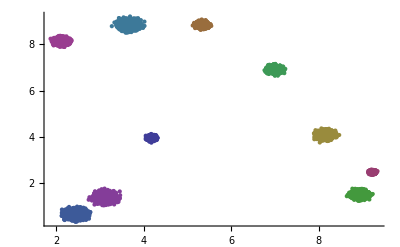

```mathematica
ListPlot[Table[Pick[trueJrL[[All,{2,3}]],sel[[i]]],{i,1,Ns}],PlotRange->All]
```

```mathematica
incs=Table[0,{i,1,Nstars}];

For[i=1,i≤Ns,i++,incs[[Flatten[Position[sel[[i]],True]]]]=RandomVariate[NormalDistribution[inclinations[[i]],2π/500],Length[Position[sel[[i]],True]]]];
```

```mathematica
Dimensions[incs]
```

{50000}

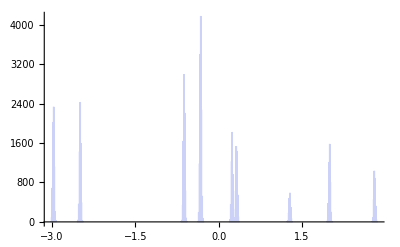

```mathematica
Histogram[incs,{-π,π,2π/500},PlotRange->All]
```

### Assign angles

```mathematica
Dimensions[initAngles=Transpose[{incs,Mod[RandomVariate[NormalDistribution[π/2,2π/500],Nstars],2π],Mod[RandomVariate[NormalDistribution[π/2,2π/500],Nstars],2π]}]]
```

{50000,3}

### Convert “initial” coordinates to configuration space (x,v) and measure satellite parameters

```mathematica
link=Install["/Users/robyn/Documents/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math"]
```

LinkObject[/Users/robyn/Documents/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math,5130,12]

```mathematica
initCart=Table[{0,0,0,0,0,0},{i,1,Nstars}];
```

```mathematica
For[i=1, i≤Nstars, i++,initCart[[i]]=AAToCart[trueActions[[i]],initAngles[[i]]]]
```

```mathematica
Uninstall[link]
```

/Users/robyn/Documents/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math

```mathematica
initPositions=initCart[[All,1;;3]];
initVelocities=initCart[[All,4;;6]]/kmsTokpcMyr;
```

```mathematica
ListPointPlot3D[initPositions,PlotRange->{{-50,50},{-50,50},{-50,50}}]
```

-Graphics3D-

```mathematica
iP=Table[Pick[initPositions,sel[[i]]],{i,1,Ns}];
```

```mathematica
ListPointPlot3D[iP,PlotRange->{{-50,50},{-50,50},{-50,50}}]
```

-Graphics3D-

```mathematica
iV=Table[Pick[initVelocities,sel[[i]]],{i,1,Ns}];
```

```mathematica
ListPointPlot3D[iV,PlotRange->All]
```

-Graphics3D-

```mathematica
meanX=Table[Mean[iP[[i]]],{i,1,Ns}]
```

{{-16.4922,11.641,16.3666},{5.85026,25.5054,16.2921},{-1.16973,28.1889,23.0705},{-11.4893,-30.7569,36.2167},{4.35557,6.87407,3.90549},{-3.32314,-38.6917,14.179},{29.1184,44.8933,12.1087},{14.7486,-18.9611,7.35805},{-37.7306,22.9128,22.5135},{-11.1252,-1.38711,6.47445}}

```mathematica
meanV=Table[Mean[iV[[i]]],{i,1,Ns}]
```

{{-78.3238,146.722,298.334},{-157.077,125.682,325.326},{-115.064,74.956,307.264},{-26.1296,-54.3691,274.218},{190.069,60.053,328.785},{-67.6172,-241.741,108.975},{200.983,139.488,70.8498},{348.178,48.7509,226.419},{-208.955,53.1221,143.45},{-187.538,103.524,329.396}}

```mathematica
dX=Table[Map[(#-meanX[[i]])&,iP[[i]]],{i,1,Ns}];
dV=Table[Map[(#-meanV[[i]])&,iV[[i]]],{i,1,Ns}];
```

```mathematica
sigX=Table[StandardDeviation[dX[[i]]],{i,1,Ns}]
```

{{0.39156,0.600783,0.367544},{0.53246,0.318377,0.380068},{1.33732,0.618839,0.751753},{1.76574,0.855301,0.584895},{0.361365,0.245973,0.359586},{1.29041,0.928249,2.67636},{1.5079,0.795128,4.19909},{0.819735,0.366406,1.12735},{2.40022,1.14295,3.2873},{0.393488,0.496044,0.426691}}

```mathematica
Map[Norm,sigX]
```

{0.805821,0.72755,1.65424,2.04731,0.56603,3.11282,4.53193,1.44123,4.22774,0.763517}

```mathematica
sigV=Table[StandardDeviation[dV[[i]]],{i,1,Ns}]
```

{{5.62973,10.094,5.30477},{7.17889,6.36217,5.24978},{17.1036,7.10304,8.31541},{13.0944,5.73526,2.92559},{22.8144,11.4605,12.6822},{9.6265,6.8711,20.557},{8.11532,4.27264,24.5697},{20.7278,7.78524,33.7473},{14.8881,6.77711,20.9337},{11.9113,23.9883,14.3539}}

```mathematica
Map[Norm,sigV]
```

{12.717,10.935,20.3011,14.5916,28.5075,23.7165,26.2256,40.3625,26.5669,30.3868}

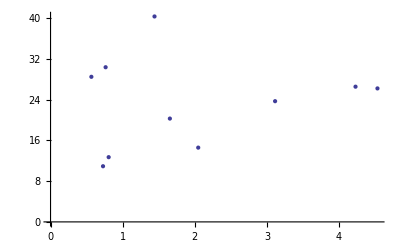

```mathematica
ListPlot[Transpose[{Map[Norm,sigX],Map[Norm,sigV]}]]
```

### Evolve angles forward in time using the frequencies

```mathematica
iA=Table[Pick[initAngles,sel[[i]]],{i,1,Ns}];

trueJrLi=Table[Pick[trueJrL,sel[[i]]],{i,1,Ns}];
```

```mathematica
iaCOM=Map[Mean,iA]
```

{{1.28438,1.5711,1.57089},{-0.620047,1.57069,1.57121},{-0.319725,1.57112,1.57072},{2.81301,1.57119,1.57073},{-0.328227,1.57064,1.57067},{-2.49406,1.5712,1.57069},{0.243637,1.57075,1.57105},{-2.97598,1.57076,1.57055},{0.3264,1.57087,1.57052},{2.00191,1.57067,1.57076}}

```mathematica
trueJrLCOM=Map[Mean,trueJrLi]
```

{{-0.369276,4.17744,3.95935},{0.525246,9.23504,2.48312},{0.396059,8.15068,4.08069},{-0.0261632,6.99779,6.90849},{-0.437684,2.44067,0.673777},{-0.873417,2.12261,8.1271},{-0.94978,5.34288,8.83412},{0.836927,8.9481,1.52359},{0.77868,3.65655,8.83005},{-0.462338,3.12299,1.38446}}

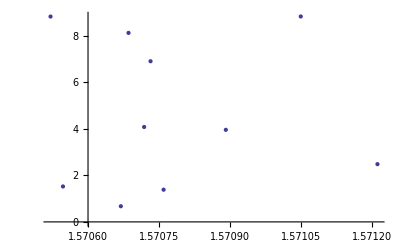

```mathematica
ListPlot[Transpose[{iaCOM[[All,3]],trueJrLCOM[[All,3]]}]]
```

#### For reference, orbital periods of stream COMs (in Myr)

```mathematica
OrbitalPds={2π/MapThread[OmegaTheta[#1,#2]&,{trueJrLCOM[[All,3]],trueJrLCOM[[All,2]]}],2π/MapThread[OmegaR[#1,#2]&,{trueJrLCOM[[All,3]],trueJrLCOM[[All,2]]}]}
```

{{36.4739,38.4598,43.4023,55.234,21.1165,55.7991,63.2847,33.9115,61.246,24.4858},{22.0093,27.3724,29.9767,36.8368,11.8526,30.8796,39.9021,23.9507,36.1955,14.1543}}

```mathematica
Transpose[OrbitalPds]//TableForm
```

36.4739 | 22.0093
38.4598 | 27.3724
43.4023 | 29.9767
55.234 | 36.8368
21.1165 | 11.8526
55.7991 | 30.8796
63.2847 | 39.9021
33.9115 | 23.9507
61.246 | 36.1955
24.4858 | 14.1543

#### Evolution time in Myr for each stream

```mathematica
eTimes=RandomReal[{500,5000},Ns]
```

{2483.64,2263.,3689.71,4384.67,2413.61,4120.89,2513.86,1113.,520.976,2422.41}

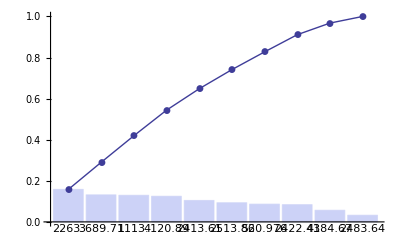

```mathematica
evolTime =eTimes[[streamIndex]];
<<StatisticalPlots`
ParetoPlot[evolTime]
```

#### Evolve the full streams forward in time

```mathematica
Dimensions[trueAngles=Transpose[{initAngles[[All,1]],Mod[initAngles[[All,2]]+Thread[OmegaTheta[trueJrL[[All,3]],trueJrL[[All,2]]]] evolTime,2π],Mod[initAngles[[All,3]]+Thread[OmegaR[trueJrL[[All,3]],trueJrL[[All,2]]]] evolTime,2π]}]]
```

{50000,3}

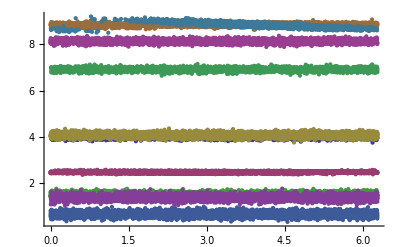

```mathematica
ListPlot[Table[Transpose[{Pick[trueAngles[[All,3]],sel[[i]]],Pick[trueJrL[[All,3]],sel[[i]]]}],{i,1,Ns}],PlotRange->{{0,2π},All}]
```

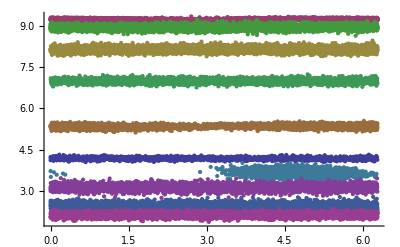

```mathematica
ListPlot[Table[Transpose[{Pick[trueAngles[[All,2]],sel[[i]]],Pick[trueJrL[[All,2]],sel[[i]]]}],{i,1,Ns}],PlotRange->{{0,2π},All}]
```

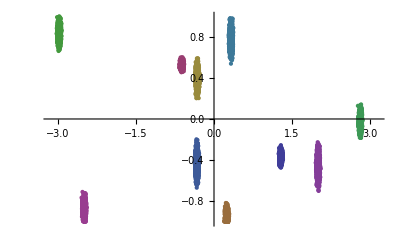

```mathematica
ListPlot[Table[Transpose[{Pick[trueAngles[[All,1]],sel[[i]]],Pick[trueJrL[[All,1]],sel[[i]]]}],{i,1,Ns}],PlotRange->{{-π,π},All}]
```

Convert coordinates to configuration space (x,v)

```mathematica
link=Install["/Users/robyn/Documents/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math"]
```

LinkObject[/Users/robyn/Documents/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math,5131,12]

```mathematica
trueCart=Table[{0,0,0,0,0,0},{i,1,Nstars}];
```

```mathematica
For[i=1, i≤Nstars, i++,trueCart[[i]]=AAToCart[trueActions[[i]],trueAngles[[i]]]]
```

```mathematica
Uninstall[link]
```

/Users/robyn/Documents/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math

```mathematica
truePositions=trueCart[[All,1;;3]];
trueVelocities=trueCart[[All,4;;6]]/kmsTokpcMyr;
```

```mathematica
tP=Table[Pick[truePositions,sel[[i]]],{i,1,Ns}];
tV=Table[Pick[trueVelocities,sel[[i]]],{i,1,Ns}];
```

```mathematica
boxsize=50;
```

```mathematica
Show[ListPointPlot3D[tP,PlotRange->{{-boxsize,boxsize},{-boxsize,boxsize},{-boxsize,boxsize}}],Graphics3D[{PointSize[Large],Yellow,Point[{{-8,0,0}}],Green,Opacity[0.1],Sphere[{-8,0,0},10],Cyan,Sphere[{-8,0,0},25],Black,Opacity[1],Thickness[0.002],Line[{{-1,0,0},{1,0,0}}],Line[{{0,-1,0},{0,1,0}}],Line[{{0,0,-1},{0,0,1}}]}],AspectRatio->1,AxesStyle->Directive[FontFamily->"Helvetica",FontSize->18],AxesLabel->{"x (kpc)","y (kpc)","z (kpc)"}]
```

-Graphics3D-

```mathematica
(*boxsize=30;*)
```

```mathematica
(*ColorData["Legacy","Panel"]*)
```

```mathematica
(*myYellow=ColorData["Legacy"]["CadmiumLemon"]*)
```

```mathematica
(*threeStreams=Show[ListPointPlot3D[{iP1,iP2,iP3},PlotStyle->{Lighter[Lighter[Red]],Lighter[Lighter[Green]],Lighter[Lighter[Blue]]},PlotRange->{{-boxsize,boxsize},{-boxsize,boxsize},{-boxsize,boxsize}}],Graphics3D[{Lighter[Red],Line[xCOM1],Lighter[Green],Line[xCOM2],Lighter[Blue],Line[xCOM3]}],ListPointPlot3D[{tP1,tP2,tP3},PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]}],Graphics3D[{Cyan,Opacity[0.2],Sphere[{-8.5,0,0},10],(*Opacity[0.1],Sphere[{-8.5,0,0},25],*)Black,Opacity[1],Thickness[0.002],Line[{{-1,0,0},{1,0,0}}],Line[{{0,-1,0},{0,1,0}}],Line[{{0,0,-1},{0,0,1}}]}],Graphics3D[{Glow[myYellow],Black,Sphere[{-8.5,0,0},2]}],AspectRatio->1,AxesStyle->Directive[FontFamily->"Helvetica",FontSize->18],AxesLabel->{"x (kpc)","y (kpc)","z (kpc)"}]*)
```

```mathematica
Dimensions[dists=Map[Norm,Transpose[{truePositions[[All,1]]-8.0, truePositions[[All,2]],truePositions[[All,3]]}]]]
```

{50000}

```mathematica
{Min[dists],Max[dists]}
```

{2.10041,75.1867}

```mathematica
(*Show[ListColorPlot[truePositions[[All,1]],truePositions[[All,3]],dists,.1,"Rainbow","x (kpc)","z (kpc)"],MyColorBar[{Min[dists],Max[dists]},5,"D"]]*)
```

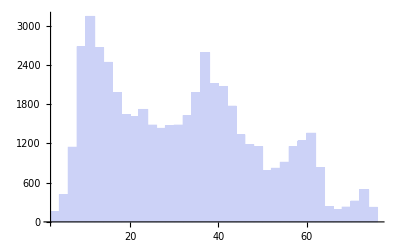

```mathematica
Histogram[dists,PlotRange->All]
```

```mathematica
DumpSave["streams10x5000.mx",{truePositions,trueVelocities,trueCart,trueJrL,trueActions,trueAngles,sel,initAngles,Nstars,Ns}];
```